# Hydorlogical System Project I

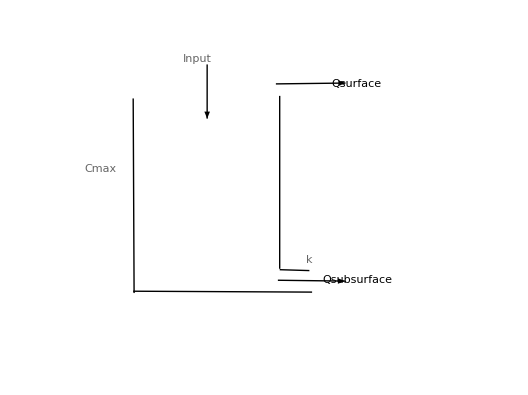
### Model Description -Graphics-

```mathematica
Simulation[input_,state_,Smax_,k_]:=Module[{noutput,nstate},
    noutput=If[input+state>Smax,input+state-Smax+k*Smax+state,k*(input+state)];
	nstate=input+state-noutput;
	Return[{noutput,nstate}]];
SequentialSimulation[Input_,Smax_,k_]:=Module[{s0=30,Input2State},
Input2State[{output_,state_},input_]:=Module[{noutput,nstate},
    noutput=If[input+state>Smax,input+state-Smax+k*Smax+state,k*(input+state)];
	nstate=input+state-noutput;
	Return[{noutput,nstate}]];
	FoldList[Input2State,{k*s0,s0},Input]];
```

### Evaluate Criterion: Square Error / Absolute Error

```mathematica
SquareError[simu_,obser_]:=Norm[Map[First,simu-obser]];
AbsoluteError[simu_,obser_]:=Norm[Map[First,simu-obser],1];
ResponseSurface[inputt_,evaluatet_]:=Module[{simu,obser,input,Smax=120,k=0.3},
  input=SequentialInputGeneration[inputt];
  obser=SequentialSimulation[input,Smax,k];
  simu[Smax_,k_]:=SequentialSimulation[input,Smax,k];
  Return[Flatten[Table[{i,j,If[evaluatet==2,SquareError[simu[j,i],obser],AbsoluteError[simu[j,i],obser]]},{i,0.1,0.5,0.01},{j,60,180,3}],1]]];
```

### Scenario Analysis

```mathematica
Scenario Generator
```

```mathematica
SequentialInputGeneration[i_]:=Module[{InputGeneration,s0=30,Smax=120,k=0.3,n=1000},
	InputGeneration[{input_,state_}]:=Module[{ninput,noutput,nstate},
		{noutput,nstate}=Simulation[input,state,Smax,k];
		ninput=If[i==1,RandomReal[{0,Smax-nstate}],
									              If[i==2,RandomReal[{Smax-nstate,(1+RandomReal[])*(Smax-nstate)}],
		            If[i==3,If[RandomReal[]<0.95,RandomReal[{0,Smax-nstate}],
			                     RandomReal[{Smax-nstate,(1+RandomReal[])*(Smax-nstate)}]],
			           If[RandomReal[]>0.5,RandomReal[{0,Smax-nstate}],
				          RandomReal[{Smax-nstate,(1+RandomReal[])*(Smax-nstate)}]]]]];
		Return[{ninput,nstate}]];
	Return[Map[First,NestList[InputGeneration,{0,s0},n]]]];
```

```mathematica
Scenario I:  state<Cmax
```

```mathematica
responseIn1=ResponseSurface[1,1];
responseIn2=ResponseSurface[1,2];
```

Response Surface of N1 Norm

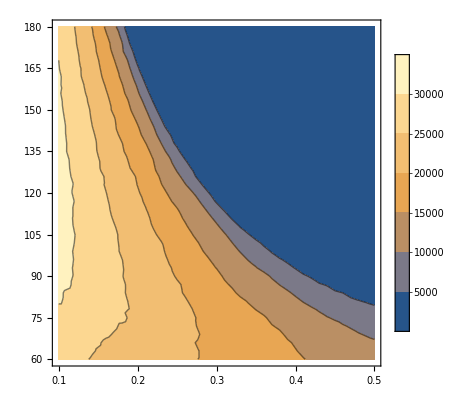

```mathematica
ListContourPlot[responseIn1,PlotLegends->Automatic]
```

Response Surface of N2 Norm

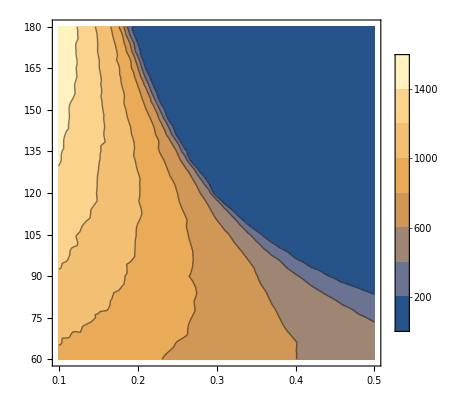

```mathematica
ListContourPlot[responseIn2,PlotLegends->Automatic]
```

```mathematica
Scenario II:  state>Cmax
```

```mathematica
responseIIn1=ResponseSurface[2,1];
responseIIn2=ResponseSurface[2,2];
```

Response Surface of N1 Norm

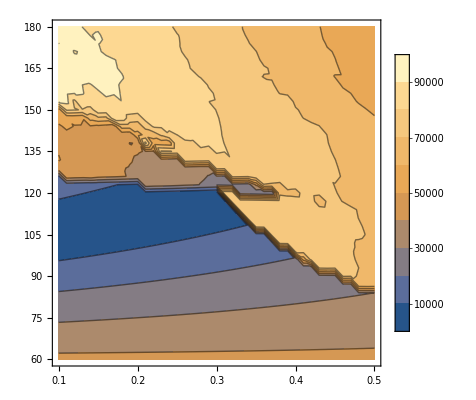

```mathematica
ListContourPlot[responseIIn1,PlotLegends->Automatic]
```

Response Surface of N2 Norm

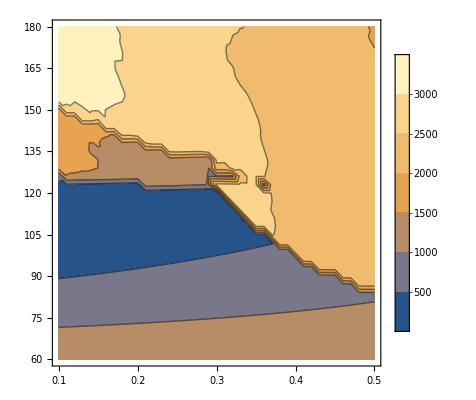

```mathematica
ListContourPlot[responseIIn2,PlotLegends->Automatic]
```

```mathematica
Scenario III:  If[t<t*,state<Cmax, state>Cmax]
```

```mathematica
responseIIIn1=ResponseSurface[3,1];
responseIIIn2=ResponseSurface[3,2];
```

Response Surface of N1 Norm

```mathematica
ListContourPlot[responseIIIn1,PlotLegends->Automatic]
```

-Graphics-

Response Surface of N2 Norm

```mathematica
ListContourPlot[responseIIIn2,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Scenario IV:  state<Cmax || state>Cmax
```

```mathematica
responseIVn1=ResponseSurface[4,1];
responseIVn2=ResponseSurface[4,2];
```

Response Surface of N1 Norm

```mathematica
ListContourPlot[responseIVn1,PlotLegends->Automatic]
```

-Graphics-

Response Surface of N2 Norm

```mathematica
ListContourPlot[responseIVn2,PlotLegends->Automatic]
```

-Graphics-